# QNM Computation and Sequential Storage

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;(* analytical value of Schwarzschild BH's n=1 QNM *)
Print["For a Schwarzschild BH: ω_0 = ", ωSBH]
```

For a Schwarzschild BH: ω_0 = 0.373672-0.0889623 ⅈ

```mathematica
(* Schwarzschild: vedere dipendenza da infinito al variare dell'ordine dell'espansione. Vedere andamento fissando uno/due parametri. Eventualmente ampliare volume esplorato *)
(* Kerr: vedere che succede con molti punti. Obiettivo futuro: variare spin e quindi qnm *)
(* ECO: per ora in pausa (vedere cosa risultati del resto) *)
```

### Tests

```mathematica
Tuples[{x,y}];Flatten[ECO[[;;]],1]//N;
```

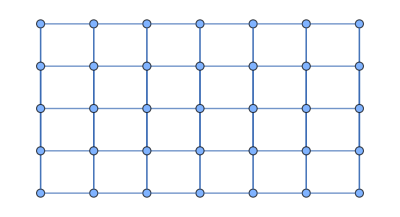

```mathematica
g=NearestNeighborGraph[Tuples[{x[[;;7]],y[[;;5]]}],{All,1/5},DistanceFunction->ManhattanDistance,GraphLayout->"BipartiteEmbedding"]
```

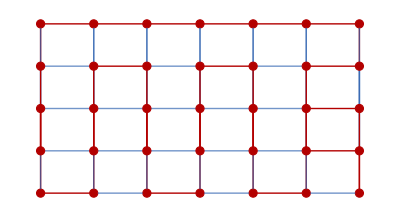

```mathematica
HighlightGraph[g,PathGraph[FindHamiltonianCycle[g,1][[1]]]]
```

```mathematica
-Graphics-//EdgeList
```

{1<->2,1<->4,2<->3,2<->5,3<->6,4<->5,4<->7,5<->6,5<->8,6<->9,7<->8,7<->10,8<->9,8<->11,9<->12,10<->11,11<->12}

```mathematica
g//EdgeList
```

{{1/8,10}<->{1/8,99/10},{1/8,10}<->{1/8,49/5},{1/8,10}<->{1/4,10},{1/8,99/10}<->{1/8,49/5},{1/8,99/10}<->{1/4,99/10},{1/8,49/5}<->{1/4,49/5},{1/4,10}<->{1/4,99/10},{1/4,10}<->{1/4,49/5},{1/4,10}<->{3/8,10},{1/4,99/10}<->{1/4,49/5},{1/4,99/10}<->{3/8,99/10},{1/4,49/5}<->{3/8,49/5},{3/8,10}<->{3/8,99/10},{3/8,10}<->{3/8,49/5},{3/8,10}<->{1/2,10},{3/8,99/10}<->{3/8,49/5},{3/8,99/10}<->{1/2,99/10},{3/8,49/5}<->{1/2,49/5},{1/2,10}<->{1/2,99/10},{1/2,10}<->{1/2,49/5},{1/2,99/10}<->{1/2,49/5}}

```mathematica
FindHamiltonianCycle[-Graphics-];
```

```mathematica
HighlightGraph[-Graphics-,First[]]
```

-Graphics-

## Grid Search

## ECO

### Parameters

```mathematica
x={};step={{1/8,2-1/8,1/8},{2+1/4,10,1/4},{2,2+1/5,1/20}};
Do[x=Union[x,Table[j,{j,i[[1]],i[[2]],i[[3]]}]],{i,step}];
x=Sort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
```

```mathematica
y={};step={{6+1/8,8,1/8}};
Do[y=Union[y,Table[j,{j,i[[1]],i[[2]],i[[3]]}]],{i,step}];
y=ReverseSort[y];ϵarray=10^-y;
```

```mathematica
ECO=Table[{h,e},{h,ηarray},{e,ϵarray}];
Print["N = ",Length[ηarray]," η_in = ",ηarray[[1]]//N," η_fin = ",ηarray[[-1]]//N ];
Print["N = ",Length[ϵarray]," ϵ_in = ",ϵarray[[1]]," ϵ_fin = ",ϵarray[[-1]] ];
```

N = 52 η_in = 0.0049757 η_fin = 0.0198944

N = 16 ϵ_in = 1/100000000 ϵ_fin = 1/(1000000 10^(1/8))

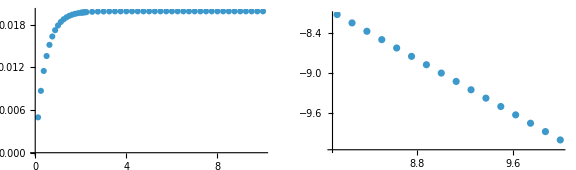

```mathematica
P1=ListPlot[Transpose[{x,ηarray}],PlotRange->All];
P2=ListPlot[Transpose[{y,ϵarray}],PlotRange->All,ScalingFunctions->"Log10"];
GraphicsGrid[{{P1,P2}},ImageSize->Large]
```

### Computation

“QNM_ECO1_heoc_9.m”: running over η.
“QNM_ECO1_heoc_10.m”: running over ϵ.
“QNM_ECO1_heoc_35.m”: running upward (1) over ϵ (+2), then upward (1) over η, adding η (+4). 
“QNM_ECO1_heoc_34.m”: running upward (1) over ϵ (+2), then downward (0) over η, adding η (+4).
“QNM_ECO1_heoc_52.m”

Legenda  per numerazione output (da file 3):
	- ϵ in prima posizione, η in seconda;
	- su quale si itera prima +2;
	- da minore a maggiore +1, viceversa +0;
	- quale si aggiunge nelle run successive +4.
	
Legenda opzioni calcolo (opt):
	1. si aggiungono nuovi valori di ϵ;
	2. si aggiungono nuovi valori di η;
	3. si itera prima su  ϵ;
	4. default (tutte false): nuovo file e si itera prima su η.

```mathematica
opt={True,False,False};
new=Table[{},{i,ηarray},{j,ϵarray}];
```

```mathematica
Which[
opt[[1]],in=Import["QNM_ECO1_heoc_53.m"];ωguess=in[[1,-1,3]](* same ηs and adding ϵs *),
opt[[2]],in=Import["QNM_ECO1_heoc_34.m"];ωguess=in[[-1,1,3]](* same ϵs and adding ηs *),
True,ωguess=(*2/5-1/10 ⅈ*)0.41029219691343865755656481837481117539`20.-0.01210110293339904243328231521370532767`20. ⅈ;(* default: new run *)];
If[opt[[3]],new=new//Transpose;ECO=ECO//Transpose(* running over ϵ then η *)];
Print["ω_guess = ",ωguess//N,"\nDim[in]",in//Dimensions,"\tDim[new] = ",new//Dimensions,"\tDim[ECO] = ",ECO//Dimensions];
```

ω_guess = 0.493874-0.0321904 ⅈ
Dim[new] = {52,16,0}	Dim[ECO] = {52,16,2}

```mathematica
(* Default: running over η then ϵ *)
Monitor[Do[Do[new[[j,i]]=Join[ECO[[j,i]],FindQNM[ωguess,ECO[[j,i]]]];
ωguess=new[[j,i,3]],{j,1,Dimensions[ECO][[1]]}];
ωguess=new[[1,i,3]],{i,1,Dimensions[ECO][[2]]}],Row[{"ij = ",{i,j}}]];

new//Dimensions
```

{52,16,4}

```mathematica
If[opt[[3]],new=new//Transpose]; 
Which[
opt[[1]],out=Join[in//Transpose,new//Transpose]//Transpose,
opt[[2]],out=Join[in,new],
True,out=new];
Print["Dim[out] = ",out//Dimensions];
```

Dim[out] = {52,32,4}

```mathematica
Export["QNM_ECO1_heoc_53.m",out];Clear[out];(* ECO1 i.e. non-rotating ECO *)
```

### Plots

```mathematica
(* da sistemare lasciare solo plot generali dell'output. Il resto da trasferire nella sezione dedicata del notebook specifico *)
```

```mathematica
in1=Import["QNM_ECO1_heoc_52.m"];
in2=Import["QNM_ECO1_heoc_53.m"];
Print["Dim[in1] = ", in1//Dimensions,"\tDim[in2] =",in2//Dimensions];
```

Dim[in1] = {52,32,4}	Dim[in2] ={52,32,4}

```mathematica
(* Real and imaginary part as function of η - remeber Extract *)
Roh1=in1[[;;,;;,1;;3;;2]]//Transpose;Roh1[[;;,;;,2]]=Re[Roh1[[;;,;;,2]]];
Ioh1=in1[[;;,;;,1;;3;;2]]//Transpose;Ioh1[[;;,;;,2]]=-Im[Ioh1[[;;,;;,2]]];
ch1=in1[[;;,;;,1;;4;;3]]//Transpose;
(* Real and imaginary part as function of ϵ *)
Roe1=in1[[;;,;;,2;;3]];Roe1[[;;,;;,2]]=Re[Roe1[[;;,;;,2]]];
Ioe1=in1[[;;,;;,2;;3]];Ioe1[[;;,;;,2]]=-Im[Ioe1[[;;,;;,2]]];
ce1=in1[[;;,;;,2;;4;;2]];
```

```mathematica
(* Real and imaginary part as function of η - remeber Extract *)
Roh2=in2[[;;,;;,1;;3;;2]]//Transpose;Roh2[[;;,;;,2]]=Re[Roh2[[;;,;;,2]]];
Ioh2=in2[[;;,;;,1;;3;;2]]//Transpose;Ioh2[[;;,;;,2]]=-Im[Ioh2[[;;,;;,2]]];
ch2=in2[[;;,;;,1;;4;;3]]//Transpose;
(* Real and imaginary part as function of ϵ *)
Roe2=in2[[;;,;;,2;;3]];Roe2[[;;,;;,2]]=Re[Roe2[[;;,;;,2]]];
Ioe2=in2[[;;,;;,2;;3]];Ioe2[[;;,;;,2]]=-Im[Ioe2[[;;,;;,2]]];
ce2=in2[[;;,;;,2;;4;;2]];
```

### Basic plots

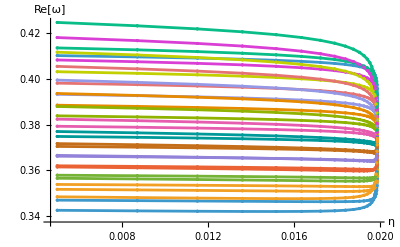

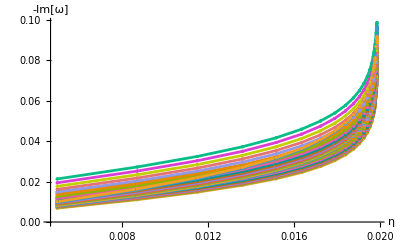

```mathematica
ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

```mathematica
in1[[24;;,1,1]]//N
```

{0.0198932,0.0198924,0.0198908,0.0198881,0.0198832,0.0198745,0.019859,0.0198315,0.0197825,0.0197688,0.0197535,0.0197363,0.0197171,0.0196954,0.0196291,0.0195406,0.0194226,0.0192653,0.0190554,0.0187756,0.0184025,0.0179049,0.0172414,0.0163566,0.0151767,0.0136032,0.011505,0.00870694,0.0049757}

```mathematica
1/(16π)//N
```

0.0198944

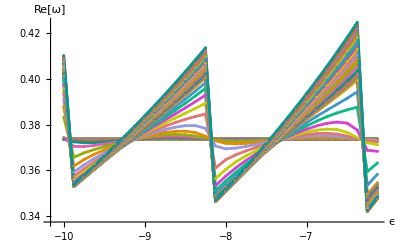

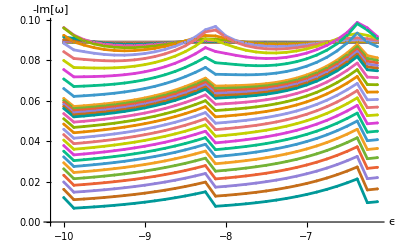

```mathematica
P1=ListPlot[Roe1[[;;,;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
P2=ListPlot[Ioe1[[;;,;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

```mathematica
Export["ReQNMvEPS_34.jpg",P1];Export["ImQNMvEPS_34.jpg",P2];
```

```mathematica
Export["eta_eps_qnm_eps10-10.m",in1[[;;,1]]];
```

```mathematica
in2[[;;,16,2]]//N
```

{7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9}

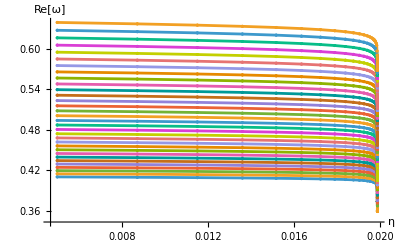

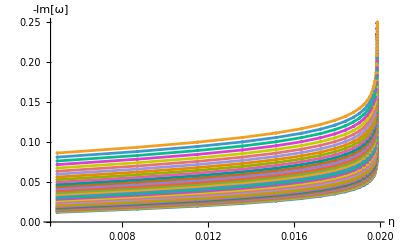

```mathematica
ListPlot[Roh2[[;;]],AxesLabel->{"η","Re[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
ListPlot[Ioh2[[;;]],AxesLabel->{"η","-Im[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

```mathematica
in2[[24,1,1]]//N
```

0.0198932

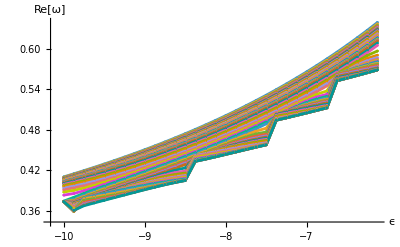

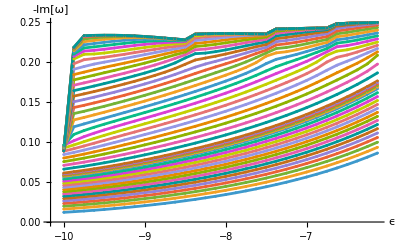

```mathematica
ListPlot[Roe2[[;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
ListPlot[Ioe2[[;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

### Specific plots

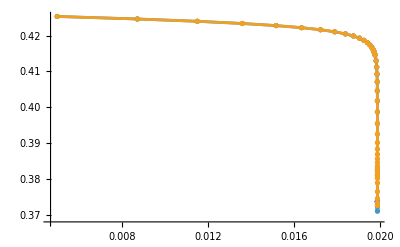

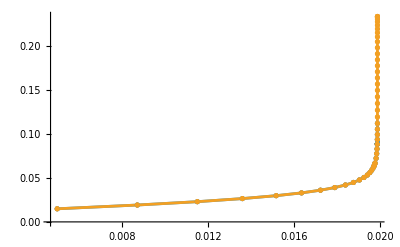

```mathematica
xrange={0.019885,0.019895};index=5;
P1=ListPlot[{Roh2[[index]],Roh1[[index]]},Mesh->Full,Joined->True,Ticks->{xrange, Automatic},PlotRange->{xrange,All}];
P2=ListPlot[{Ioh2[[index]],Ioh1[[index]]},Mesh->Full,Joined->True,Ticks->{xrange,Automatic},PlotRange->{xrange,All}];

ListPlot[{Roh2[[index]],Roh1[[index]]},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P1,Scaled[{0.15,0.15}],Scaled[{0,0}]]]
ListPlot[{Ioh2[[index]],Ioh1[[index]]},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P2,Scaled[{0.15,0.5}],Scaled[{0,0}]]]
(*{{0.01989,0.0199},All}*)
```

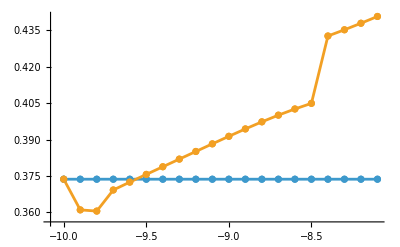

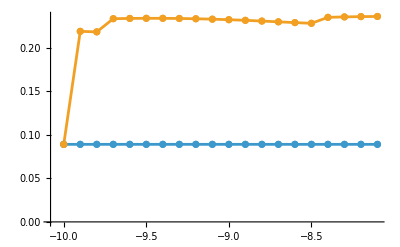

```mathematica
xrange={0.019885,0.019895};
P1=ListPlot[Roe2[[-1,;;20]],ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,Ticks->{None,Automatic},PlotRange->All];
P2=ListPlot[Ioe2[[-1,;;20]],ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,Ticks->{None,Automatic},PlotRange->All];

ListPlot[{Roe2[[-1,;;20]],Roe1[[-1]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P1,Scaled[{0.2,0.6}],Scaled[{0,0}]]]
ListPlot[{Ioe2[[-1,;;20]],Ioe1[[-1]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P2,Scaled[{0.55,0.45}],Scaled[{0,0}]]]
(*{{0.01989,0.0199},All}*)
```

```mathematica
Roh2//Dimensions
```

{40,52,2}

```mathematica
Roh1//Dimensions
```

{49,24,2}

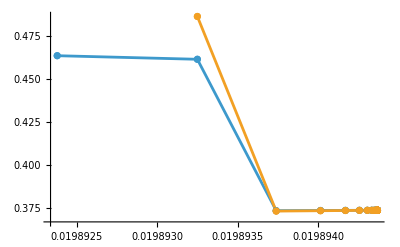

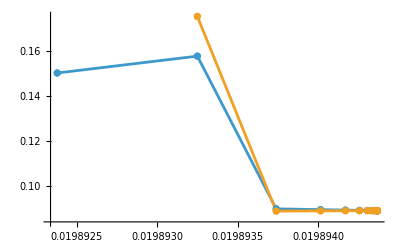

```mathematica
xrange={0.01989,0.019895};index=20;
ListPlot[{Roh2[[index,28;;]],Roh1[[index]]},Mesh->Full,Joined->True,PlotRange->All]
ListPlot[{Ioh2[[index,28;;]],Ioh1[[index]]},Mesh->Full,Joined->True,PlotRange->All]
(*{{0.01989,0.0199},All}*)
```

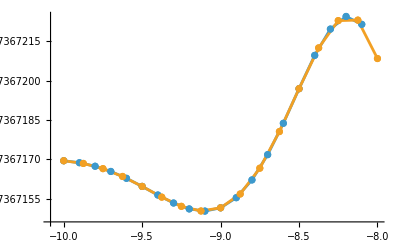

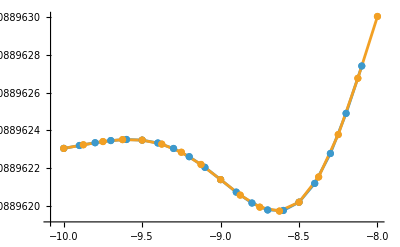

```mathematica
ListPlot[{Roe2[[-1,;;20]],Roe1[[1,;;17]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All(*{{Automatic,10^-8},{0.37367,0.373673}}*)]
ListPlot[{Ioe2[[-1,;;20]],Ioe1[[1,;;17]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All(*{{Automatic,10^-8},{0.08896,0.08897}}*)]
```

## Kerr

### Spin

```mathematica
χarray={10^-2,5 10^-2,10^-1,15 10^-2,2 10^-1,25 10^-2,3 10^-1};
ωtrue={0.3749365685-0.08894183057ⅈ,0.3801455748-0.08884890191ⅈ,0.3870175384-0.08870569903ⅈ,0.3943329877-0.08852826817ⅈ,0.4021453242-0.08831116621ⅈ,0.4105179098-0.08804765025ⅈ,0.4195266818-0.08772927189ⅈ};
(*ωguess={};*)
```

### Computation

```mathematica
ωfound=Table[{},{i,χarray}];ωguess=0.4-0.1 ⅈ;
Monitor[Do[ωfound[[i]]={χarray[[i]],ωtrue[[i]],FindQNM[ωguess,χarray[[i]]][[1]]};ωguess=ωfound[[i,-1]],
{i,1,Length[χarray]}],Row["Iteration: i = ",i]];
```

```mathematica
Export["QNM_Kerr_generale.m",ωfound]
```

QNM_Kerr_generale.dat

```mathematica
(* con ordHor=3
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

```mathematica
(* con ordHor=7
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

## Random Search

```mathematica
RandomSearch[par_,ops_,ranges_,finder_,n_]:=Module[{data,theta,Δω},
data={};
Monitor[Do[
theta=MapThread[#1[#2]&,{ops,RandomVariate[UniformDistribution[#]]&/@ranges}];
Δω=finder[par[[1]],par[[3;;]],theta][[1]]-par[[2]];
AppendTo[data,Join[theta,{Re[Δω],Im[Δω]}]],{i,n}],Row[{"Iteration: i = ",i}]];
Return[data];
];
```

## Schwarzschild (eps, match, inf)

```mathematica
data={};n=250;
Module[{ϵ,μ,ι,ωfound,check},Monitor[Do[
ϵ=10^-7(*RandomVariate[UniformDistribution[{-7,-3}]]*);μ=RandomVariate[UniformDistribution[{5,15}]];ι=60(*RandomVariate[UniformDistribution[{25,150}]]*);
ωfound=FindQNM[ωguess,{2,ϵ,μ,ι}][[1]];
AppendTo[data,{ϵ,μ,ι,ωfound,Abs[ωfound-ωSBH]}],
{i,n}],Row[{"Iteration: i = ",i}]]];
data=Sort[data,#1[[-1]]<#2[[-1]]&];
Print["Dim[data] = ",data//Dimensions];
```

Dim[data] = {250,5}

```mathematica
Export["QNM_data/QNM_Schw_emiod_10_5.m",data];Clear[data,n];
```

## Kerr (eps, match, inf)

```mathematica
FindQNM[ωguess_,par_,theta_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,par[[1]],theta,coefHor,coefInf][[1]];(* watch out for differences in input parameters *)
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20(*,EvaluationMonitor:>Print["ω = ", x," Δψ' = ",Abs[g[x]]]*)][[1]];
Return[{ωroot,Abs[g[ωroot]]}];
];
```

```mathematica
data=RandomSearch[{33/100-88/1000 ⅈ,ωSBH,0},{10^#&,#&,#&},{{-10,-4},{5,5},{40,80}},FindQNM,500];
Print["Dim[data] = ",data//Dimensions];
```

Dim[data] = {500,5}

```mathematica
(* Second term tells the spin, third the output type, and fourth the run (potentially with different values) *)
Export["QNM_data\\Kerr_0_emidRdI_3.m",data];Clear[data];
```

## ECO

### Hyperparameters (match, inf)

```mathematica
ECO={1/(16π),10^-10};ωguess=2/5-1/10 ⅈ;
```

```mathematica
FindQNM[ωguess_,theta_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,ECO,theta,coefInf][[1]];(* watch out for differences in input parameters *)
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20(*,EvaluationMonitor:>Print["ω = ", x," Δψ' = ",Abs[g[x]]]*)][[1]];
Return[{ωroot,Abs[g[ωroot]]}];
]
```

```mathematica
data={};n=1000;
Module[{μ,ι,ωfound,check},Monitor[Do[μ=RandomVariate[UniformDistribution[{5,15}]];ι=RandomVariate[UniformDistribution[{30,150}]];
ωfound=FindQNM[ωguess,{2,μ,ι}][[1]];
AppendTo[data,{μ,ι,ωfound,Abs[ωfound-ωSBH]}],
{i,n}],Row[{"Iteration: i = ",i}]]];
data=Sort[data,#1[[-1]]<#2[[-1]]&];
Print["Dim[data] = ",data//Dimensions];
```

Dim[data] = {1000,4}

```mathematica
Export["QNM_ECO1_miod_3.m",data];Clear[data,n];
```